```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CloseKernels[];
LaunchKernels[52];
$KernelCount
```

52

# Pre

```mathematica
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd3xf[mf2_,q_,T_,μ_]:=-nff[mf2,q,T,μ]/T^3+(7 nff[mf2,q,T,μ]^2)/T^3-(12 nff[mf2,q,T,μ]^3)/T^3+(6 nff[mf2,q,T,μ]^4)/T^3;
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
nfd3xa[mf2_,q_,T_,μ_]:=-nfa[mf2,q,T,μ]/T^3+(7 nfa[mf2,q,T,μ]^2)/T^3-(12 nfa[mf2,q,T,μ]^3)/T^3+(6 nfa[mf2,q,T,μ]^4)/T^3;
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
h=6.5;
λ=75.8;
ν=-482.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=300;
```

# Mean-field wave function renormalization

## threshold functions and equations

```mathematica
F2[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
F4[q_,ρ_,h_,T_,μ_]:=1/6 q^6 (-(9 q (-nfd1xa[mf2[h,ρ],q,T,μ]/(2 √(q^2+mf2[h,ρ]))-nfd1xf[mf2[h,ρ],q,T,μ]/(2 √(q^2+mf2[h,ρ]))))/(8 (q^2+mf2[h,ρ])^(5/2))+(3 q (nfd1xa[mf2[h,ρ],q,T,μ]/(4 (q^2+mf2[h,ρ])^(3/2))+nfd1xf[mf2[h,ρ],q,T,μ]/(4 (q^2+mf2[h,ρ])^(3/2))-nfd2xa[mf2[h,ρ],q,T,μ]/(4 (q^2+mf2[h,ρ]))-nfd2xf[mf2[h,ρ],q,T,μ]/(4 (q^2+mf2[h,ρ]))))/(4 (q^2+mf2[h,ρ])^(3/2))-1/(2 √(q^2+mf2[h,ρ]))q (-(3 nfd1xa[mf2[h,ρ],q,T,μ])/(8 (q^2+mf2[h,ρ])^(5/2))-(3 nfd1xf[mf2[h,ρ],q,T,μ])/(8 (q^2+mf2[h,ρ])^(5/2))+(3 nfd2xa[mf2[h,ρ],q,T,μ])/(8 (q^2+mf2[h,ρ])^2)+(3 nfd2xf[mf2[h,ρ],q,T,μ])/(8 (q^2+mf2[h,ρ])^2)-nfd3xa[mf2[h,ρ],q,T,μ]/(8 (q^2+mf2[h,ρ])^(3/2))-nfd3xf[mf2[h,ρ],q,T,μ]/(8 (q^2+mf2[h,ρ])^(3/2)))+(15 q (0.-nfa[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],q,T,μ]))/(16 (q^2+mf2[h,ρ])^(7/2)));
Zrhothr[ρ_,h_,T_,μ_]:=-(h^2 Nc)/π^2 NIntegrate[1/q(-F2[q,ρ,h,T,μ]+(4/3)F3[q,ρ,h,T,μ]-8/15 F4[q,ρ,h,T,μ]),{q,0.,15000.},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10,WorkingPrecision->13];
Zrhovac[ρ_,h_,M_]:=-(Nc h^2)/(12 π^2)Log[(√mf2[h,ρ])/M];
Za1thr[ρ_,h_,T_,μ_]:=-(h^2 Nc)/π^2 NIntegrate[1/q(-F2[q,ρ,h,T,μ]+(4/3+((*2*)mf2[h,ρ])/q^2)F3[q,ρ,h,T,μ]-8/15 F4[q,ρ,h,T,μ]),{q,0.,15000.},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10,WorkingPrecision->13];
Za1vac[ρ_,h_,M_]:=-(Nc h^2)/(12 π^2)Log[(√mf2[h,ρ])/M];
Zsigmathr[ρ_,h_,T_,μ_]:=(h^2 Nc)/π^2 NIntegrate[1/q(F2[q,ρ,h,T,μ]-((2mf2[h,ρ])/q^2+2/3)F3[q,ρ,h,T,μ]+8/3 mf2[h,ρ]/q^2 F4[q,ρ,h,T,μ]),{q,0.,15000.},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10,WorkingPrecision->13];
Zsigmavac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[h,ρ])/M];
Zetathr[ρ_,h_,T_,μ_]:=(h^2 Nc)/π^2 NIntegrate[1/q(F2[q,ρ,h,T,μ]-2/3 F3[q,ρ,h,T,μ]),{q,0.,15000.},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10,WorkingPrecision->13];
Zetavac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[h,ρ])/M];
Zpisthr[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2[q,ρ,h,T,μ]+2/3 F3[q,ρ,h,T,μ]),{q,0.,500.,10000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
Zpisvac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[h,ρ])/M];
```

## Z_ρ data

```mathematica
sigmadata=Flatten[Import["./sigmaT50_mu.dat"]];
mudata=Flatten[Import["./mu5to500.dat"]];
```

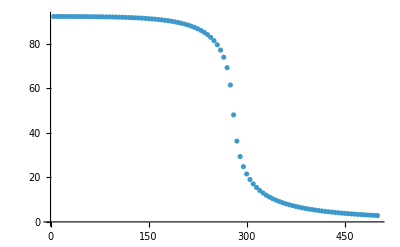

```mathematica
ListPlot[Transpose[{mudata,sigmadata}],PlotRange->All]
```

```mathematica
Zrho[ρ_,h_,T_,μ_,M_]:=Zrhothr[ρ,h,T,μ]+Zrhovac[ρ,h,M]+1.;
```

```mathematica
Zrho=Flatten[ParallelTable[Zrho[sigmadata[[i]]^2/2,h,N[50],N[i]*5,300.]//Quiet,{i,1,100,1}]];
```

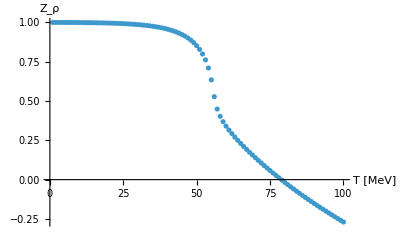

```mathematica
plotvac=ListPlot[{Zrho},PlotRange->All,AxesLabel->{"T [MeV]","Z_ρ"},PlotRange->All]
```

```mathematica
Export["./Zrho_T50_mu.dat",Zrho];
```

## Z_a1 data

```mathematica
Za1[ρ_,h_,T_,μ_,M_]:=Za1thr[ρ,h,T,μ]+Za1vac[ρ,h,M]+1.;
```

```mathematica
Za1data=Flatten[ParallelTable[Za1[sigmadata[[i]]^2/2,h,N[50],N[i]*5,300.]//Quiet,{i,1,100,1}]];
```

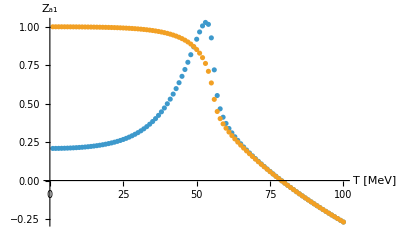

```mathematica
plotvac=ListPlot[{Za1data-(Za1data[[100]]-Zrho[[100]]),Zrho},PlotRange->All,AxesLabel->{"T [MeV]","Z_a1"},PlotRange->All]
```

```mathematica
Export["./Za1_T50_mu.dat",Za1data];
```

## Z_σ data

```mathematica
Zsigma[ρ_,h_,T_,μ_,M_]:=(Zsigmathr[ρ,h,T,μ]+Zsigmavac[ρ,h,M])+1.;
```

```mathematica
Zsigmadata=Flatten[ParallelTable[Zsigma[sigmadata[[i]]^2/2,h,N[50],N[i]*5,300.]//Quiet,{i,1,100,1}]];
```

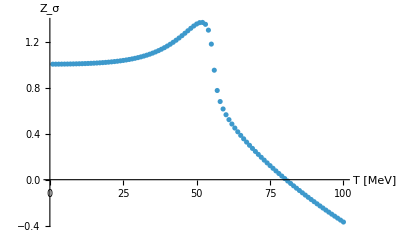

```mathematica
plotvac=ListPlot[{Zsigmadata},PlotRange->All,AxesLabel->{"T [MeV]","Z_σ"},PlotRange->All]
```

```mathematica
Export["./Zsigma_T50_mu.dat",Zsigmadata];
```

## Z_η data

```mathematica
Zfeta[ρ_,h_,T_,μ_,M_]:=Zetathr[ρ,h,T,μ]+Zetavac[ρ,h,M]+1.;
```

```mathematica
Zetadata=Flatten[ParallelTable[Zfeta[sigmadata[[i]]^2/2,h,N[50],N[i]*5,300.]//Quiet,{i,1,100,1}]];
```

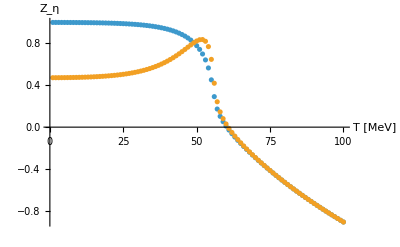

```mathematica
plotvac=ListPlot[{Zetadata,Zsigmadata-(Zsigmadata[[100]]-Zetadata[[100]])},PlotRange->All,AxesLabel->{"T [MeV]","Z_η"},PlotRange->All]
```

```mathematica
Export["./Zeta_T50_mu.dat",Zetadata];
```